# Лабораторная работа №5

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    6 октября 2021

## Задание 1

### 2.2

Спроектируйте глобальные правила ExprAsTree построения дерева выражения рекурсивным способом и опишите связи между этими правилами.

```mathematica
ExprAsTree[expr_, options___Rule]:= Graphics[ExprAsTree[expr,{0,0}],options]
```

Внешняя функция пользователя.

```mathematica
ExprAsTree[atom_?AtomQ, coord :{_,_}]:={Text[atom,coord]}
```

Внутрення (техническая) функция готовит графические объекты для отображения узлов и ребер графа.
ExprAsTree[atom_?AtomQ,coord:{_,_}] - для атомарного выражения.
ExprAsTree[expr_,{x_,y_}] - для неатомарного выражения.

```mathematica
ExprAsTree[-1+2 ⅈ,{0,0}]
```

{Text[-1+2 ⅈ,{0,0}]}

```mathematica
-1+2 ⅈ//TreeForm
```

-Graphics-

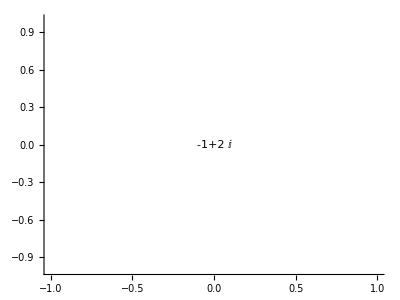

```mathematica
ExprAsTree[-1+2 ⅈ,Axes->True,BaseStyle->{FontWeight->Bold}]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:= {Text[Head[expr],{x,y}]}
```

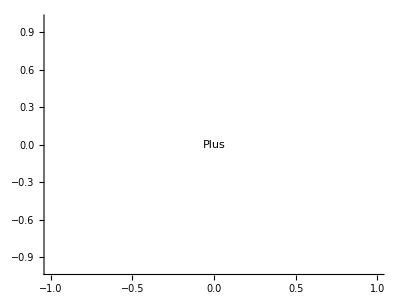

```mathematica
ExprAsTree[a+2 ⅈ,Axes->True,BaseStyle->{FontWeight->Bold}]
```

### 2.3

Постройте функцию NodesCoord, которая по заданной 
координате (x, y) корневого узла дерева выражения expr вычисляет 
координаты корневых узлов поддеревьев или листьев, соответствующих аргументам выражения expr.

```mathematica
ClearAll[Width];
```

```mathematica
Width[_?AtomQ]=1;
```

```mathematica
Width[expr_]:=Plus@@Width/@List@@(expr)
```

Если выражение, на которое действует Width - атом, то Width вычисляется и возвращает значение 1. Иначе Width представляет выражение в виде списка аргументов и действует на каждый из них.

```mathematica
Width/@List@@(1/(a^5+b)-x^9+57-v)
```

{1,4,2,3}

Результатом вычисления Width является количество атомов заданного выражения.

```mathematica
FoldList[Plus,0,Width/@List@@(1/(a^5+b)-x^9+57-v)]
```

{0,1,5,7,10}

```mathematica
FoldList[Plus,0,Width/@List@@(1/(a^5+b)-x^9+57-v)]//Most
```

{0,1,5,7}

```mathematica
{x+#,y-1}&/@FoldList[Plus,0,Width/@List@@(1/(a^5+b)-x^9+57-v)]//Most
```

{{x,-1+y},{1+x,-1+y},{5+x,-1+y},{7+x,-1+y}}

```mathematica
NodesCoord[expr_,{x_,y_}](*функция,которая по заданной
координате (x,y) корневого узла дерева неатомарного выражения expr вычисляет координаты корневых узлов поддеревьев,соответствующих аргументам выражения expr.*):={x+#,y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

```mathematica
?NodesCoord
```

```mathematica
NodesCoord[1/(a^5+b)-x^9+57-v,{0,0}]
```

{{0,-1},{1,-1},{5,-1},{7,-1}}

```mathematica
NodesCoord[x-5 y+z^2,{0,0}]
```

{{0,-1},{1,-1},{3,-1}}

```mathematica
expr=1/(a^5+b)-x^9+57-v
```

57+1/(a^5+b)-v-x^9

### 2.4

```mathematica
ExprAsTree[expr_,{x_,y_}]:={Text[Head[expr],{x,y}], MapThread[ExprAsTree[#1(*что отображать*),#2(*где отображать*)]&,{List@@(expr),NodesCoord[expr, {x,y}]}](*список аргументовЮ список координат соответствующих корневых узлов*)}
```

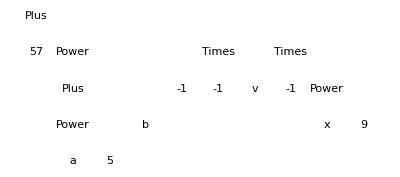

```mathematica
ExprAsTree[expr,BaseStyle->{FontWeight->Bold}]
```

### 2.5-2.6

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Black,Line[{{x,y},#}](*модифицировали функцию так, чтобы она отображала соединительные линии*)&/@ NodesCoord[expr,{x,y}]},{Text[Framed[Head[expr]],{x,y}](*модифицировали функцию так, чтобы она отображала ребра графа*)}, MapThread[ExprAsTree[#1,#2]&,{List@@(expr),NodesCoord[expr, {x,y}]}]}
```

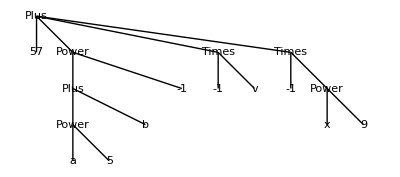

```mathematica
ExprAsTree[expr]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Green,Line[{{x,y},#}]&/@ NodesCoord[expr,{x,y}]},{Background-> LightGreen,Text[Framed[Head[expr]],{x,y}]}, MapThread[ExprAsTree[#1,#2]&,{List@@(expr),NodesCoord[expr, {x,y}]}]}
```

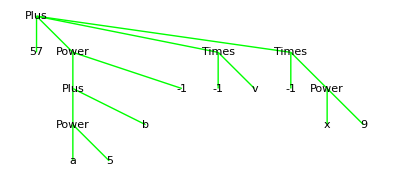

```mathematica
ExprAsTree[expr]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Green,Line[{{x,y},#}]&/@ NodesCoord[expr,{x,y}]},{Background-> LightGreen,Text[Framed[Head[expr]]//Tooltip(*модифицировали функцию так, чтобы при наведении указателя Мыши на корневой узел всплывала подсказка*),{x,y}]}, MapThread[ExprAsTree[#1,#2]&,{List@@(expr),NodesCoord[expr, {x,y}]}]}
```

```mathematica
ExprAsTree[expr]
```

-Graphics-

### 2.7

```mathematica
NodesCoord[expr_,{x_,y_}]:=({x-((Width[expr]-1)/2)(*смещение по оси иксов всех корневых узлов подвыражений*)+#, y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most)+(*вычисляем координаты поддеревьев отн-но дерева с координатами (х,у) с учетом центровки*)({((Width[#]-1)/2),0}&/@List@@expr)
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Black,Line[{{x,y},#}]&/@NodesCoord[expr,{x,y}]},Tooltip[{Background-> LightGreen,Text[Framed[Head[expr]],{x,y}]},expr//TraditionalForm], MapThread[ExprAsTree[#1,#2]&,{#,NodesCoord[expr,{x,y}]}&[List@@expr]]}
```

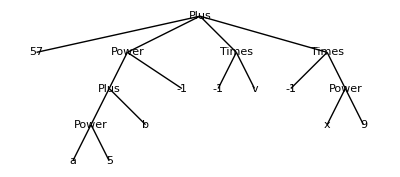

```mathematica
expr//ExprAsTree
```

```mathematica
expr
```

57+1/(a^5+b)-v-x^9

```mathematica
NodesCoord[{"Встроенные типы объектов","Числа", "Коллекции"},{0,0}]
```

{{-1,-1},{0,-1},{1,-1}}

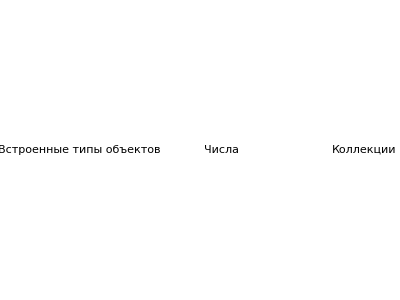

```mathematica
Graphics[MapThread[Text[#1,#2]&,{{"Встроенные типы объектов","Числа", "Коллекции"},{{-1,-1},{0,-1},{1,-1}}}]]
```

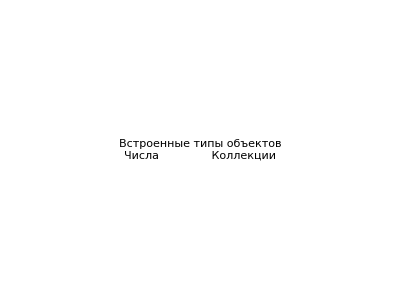

```mathematica
ExprAsTree["Встроенные типы объектов
Числа               Коллекции
"]
```

## Задание 2

### 1.1

```mathematica
funcFibonacci[1]:=0
funcFibonacci[2]:=1
funcFibonacci[n_]:=Plus[funcFibonacci[n-2],funcFibonacci[n-1]]
```

```mathematica
funcFibonacci[7]
```

8

```mathematica
funcFibonaccis[q_]:=Table[funcFibonacci[n],{n,q}]
```

```mathematica
funcFibonaccis[13]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144}

```mathematica
?funcFibonaccis
```

### 1.2

```mathematica
Ackerman[0,n_]:=n+1
```

```mathematica
Ackerman[m_,0]:=Ackerman[m-1,1]
```

```mathematica
Ackerman[m_,n_]:=Ackerman[m-1,Ackerman[m,n-1]]
```

```mathematica
Ackerman[3,3]
```

61

```mathematica
?Ackerman
```

```mathematica
Ackermans[t_,k_]:=Table[Ackerman[m,n],{m,0,t},{n,0,k}]
```

```mathematica
Ackermans[3,3]
```

{{1,2,3,4},{2,3,4,5},{3,5,7,9},{5,13,29,61}}

```mathematica
ListPlot3D[Ackermans[3,3]]
```

-Graphics3D-

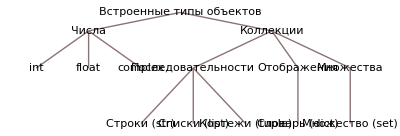

```mathematica
TreeForm["Встроенные типы объектов"["Числа"["int", "float", "complex"], "Коллекции"["Последовательности"["Строки (str)","Списки (list)","Кортежи (tuple)"], "Отображения"["Словарь (dict)"], "Множества"["Множество (set)"]]],LayerSizeFunction->(#&),PlotStyle->{Background-> LightGreen}]
```

```mathematica
TreeForm["Встроенные типы объектов"["Числа"["int", "float", "complex"], "Коллекции"["Последовательности"["Строки (str)","Списки (list)","Кортежи (tuple)"], "Отображения"["Словарь (dict)"], "Множества"["Множество (set)"]]]],LayerSizeFunction->(#&),PlotStyle->{Background-> LightGreen}]
```